```mathematica
(* FROZEN WAVES SUPERFICIAIS ESCALARES - MEIOS SEM PERDAS *)
```

```mathematica
(* ############################### Parâmetros gerais ############################### *)

(* SIP *)
F1[z_]:=Piecewise[{{1.0,0.4≤ z≤0.6}}]
F2[z_]:=Piecewise[{{1.0,0.25≤ z≤0.75}}]
F3[z_]:=Piecewise[{{1.0,0.3≤ z≤0.7}}]
F4[z_]:=Piecewise[{{1.0,0.35≤ z≤0.65}}]
F[z_]:={F1[z],F1[z],F2[z],F3[z],F4[z],F1[z]}

(* Parâmetros *)
λ=532. 10^-9;
k=2π/λ;
Q=0.999996k;
L=4.0;(* Comprimento L *)
NN=20; (* 2NN+1 feixes de Bessel para cada LFW *)
MM=6; (* Número de LFWs *)

(* Números de onda *)
β[n_]:=Q+2π n/L
kρ[n_]:=√(k^2-β[n]^2)

(* Espaçamento radial entre as LFWs *)
Δρmin=2.405/√(k^2-Q^2); (* Largura do maior spot das LFWs *)
Δρ=10*Δρmin;(* Separação radial entre as LFWs *)

(* Deslocamento de cada LFW com relaçao à origem *)
ρ0[m_]:=m Δρ;
ϕ0=0.;

(* Print dos parâmetros gerais *)
Print["### Parâmetros ##################\n",
"λ = ",λ*10^9," nm","\n","k = ",k," m^-1","\n", "Q = ",Q," m^-1","\n","L = ",L*10^2," cm","\n","NN = ",NN,"\n", "MM = ",MM]

Print["### Espaçamento entre as LWFs ####\n",
"Δρmin = ",EngineeringForm[Δρmin]," m","\n","Δρ    = ",EngineeringForm[Δρ]," m","\n","Δρ/Δρmin = ",Δρ/Δρmin, "\nLFW/pixel = ", MM]

Print["### Ângulos de áxicon ###########\n",
"α0_-NN = ",(180/Pi)ArcSin[kρ[-NN]/k],"°","\n","α0_0  = ",(180/Pi)ArcSin[kρ[0]/k],"°","\n","α0_NN  = ",(180/Pi)ArcSin[kρ[NN]/k],"°"]
```

### Parâmetros ##################
λ = 532. nm
k = 1.18105×10^7 m^-1
Q = 1.18105×10^7 m^-1
L = 400. cm
NN = 20
MM = 6

### Espaçamento entre as LWFs ####
Δρmin = 143.99×10^-6 m
Δρ    = 719.95×10^-6 m
Δρ/Δρmin = 5.
LFW/pixel = 6

### Ângulos de áxicon ###########
α0_-NN = 0.20911°
α0_0  = 0.162057°
α0_NN  = 0.0937972°

### Plot F(y,z)  ###########

```mathematica
(* ##################################### SFWs ##################################### *)
```

```mathematica
(* Coeficientes A[[n,pxh]] *)
A=1/L Table[NIntegrate[F[z][[m]]Exp[ⅈ(2 π n/L)z],{z,0,L},AccuracyGoal->6,MaxRecursion->4],{n,-NN,NN},{m,1,MM}];
```

```mathematica
(* Função SFW *)
SΨ[ρ_,ϕ_,z_]:=∑_(m=1)^MM (∑_(n=-NN)^NN A[[n+NN+1,m]]BesselJ[0,kρ[n] √(ρ^2+ρ0[m]^2-2ρ ρ0[m] Cos[ϕ-ϕ0])]Exp[-ⅈ β[n]z])
```

```mathematica
(* ##################################### Plots ##################################### *)
```

```mathematica
DensityPlot[Abs[SΨ[ρ 10^-3,0,z 10^-2 ]]^2,{z,-10.,110.},{ρ,-0.5,(7Δρ*10^3+0.5)},Mesh->None,PlotPoints->100,PlotRange->All,ColorFunction->ColorData["AvocadoColors"],PlotLegends->Automatic,PlotLabel->"|ψ_SFW(ρ,0,z)|^2",FrameLabel->{"z (cm)","ρ (mm)"},FrameTicks->{{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"},{4,"4.0"},{5,"5.0"}},None},{Automatic,None}},BaseStyle->{FontFamily->"Times",FontSize->20,FontWeight->"Plain"},LabelStyle->{FontFamily->"Times",FontSize->20,FontWeight->"Plain"}]
```

-Graphics-

```mathematica
im2=Out[106];
```

```mathematica
F1[z_]:=Piecewise[{{1.0,0.4≤ z≤0.6}},-3]
F2[z_]:=Piecewise[{{1.0,0.25≤ z≤0.75}},-3]
F3[z_]:=Piecewise[{{1.0,0.3≤ z≤0.7}},-3]
F4[z_]:=Piecewise[{{1.0,0.35≤ z≤0.65}},-3]
F[z_]:={F1[z],F1[z],F2[z],F3[z],F4[z],F1[z]}
```

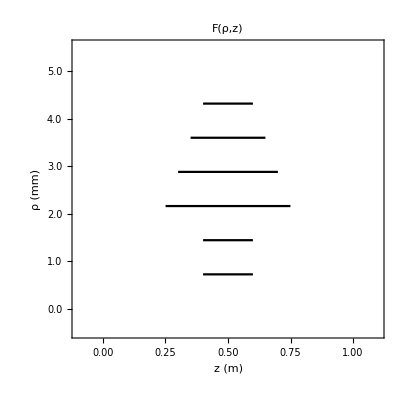

```mathematica
Plot[{10^3 ρ0[1]F1[z],10^3 ρ0[2]F1[z],10^3 ρ0[3]F2[z],10^3 ρ0[4]F3[z],10^3 ρ0[5]F4[z],10^3 ρ0[6]F1[z]},{z,-.10,1.10},PlotRange->{-0.501,(7.0Δρ*10^3+0.5)},PlotLabel->"F(ρ,z)",FrameLabel->{"z (m)","ρ (mm)"},FrameTicks->{{{{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"},{4,"4.0"},{5,"5.0"}},None},{Automatic,None}},BaseStyle->{FontFamily->"Times",FontSize->20,FontWeight->"Plain"},LabelStyle->{FontFamily->"Times",FontSize->20,FontWeight->"Plain"},Frame->True, AspectRatio->1,PlotStyle->Black]
```